# Hardware Verification Workflow with SCR1

## What is the project?

We developed a driver for SCR1 based on Device  Framework

SCR1  is
 - Open-source microcontroller core
 - RISC-V architecture (RV32I|E[MC])
 github.com/syntacore/scr1
 
 RISCV — open computer architecture riscv.org

#### Structure of SCR1

Why do we need this project?

How to use the SCR1 driver

#### Initialization

```mathematica
SetDirectory[NotebookDirectory[]];
Needs["SCR1Device`"];
```

#### Connect SCR1

```mathematica
device = DeviceOpen["SCR1"]
```

DeviceObject[…]

#### Disconnect SCR1

```mathematica
DeviceClose[device]
```

#### Reset SCR1 (load a program to the SCR1 memory)

```mathematica
DeviceRead[device,{
"reset","/Users/ckorikov/_syntacore/projects/wolfram_russianhack18_scr1/cpp_bridge/dhrystone.bin"
}]
```

0

#### Step by step program evaluation

```mathematica
DeviceRead[device,"next_ipc"]
```

516

#### Execution graph

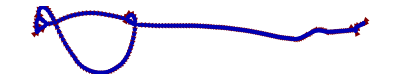

```mathematica
DeviceRead[device,{
"reset","/Users/ckorikov/_syntacore/projects/wolfram_russianhack18_scr1/cpp_bridge/dhrystone.bin"
}];
ipcList = Table[DeviceRead[device,"next_ipc"],10000];g=Union[BlockMap[#[[1]]->#[[2]]&,ipcList,2,1]];
GraphPlot[g,DirectedEdges-> True]
```

#### Read registers

```mathematica
Dataset[
Table[
{i,BaseForm[#,16],BaseForm[#,2]}&@DeviceRead[device,{"get_reg",i}] ,
{i,1,31}
]
]
```

Dataset[<>]

#### Animation with register changes

```mathematica
DeviceRead[device,{
"reset","/Users/ckorikov/_syntacore/projects/wolfram_russianhack18_scr1/cpp_bridge/dhrystone.bin"
}];
```

```mathematica
Table[DeviceRead[device,"next_ipc"],12000];
ListAnimate[Table[DeviceRead[device,"next_ipc"];MatrixPlot[BlockMap[#&,Map[#[[2]]&,Table[{i,DeviceRead[device,{"get_reg",i}]},{i,1,31}]],6],ColorFunction->"SunsetColors"],
1000
]]
```

#### Read the memory

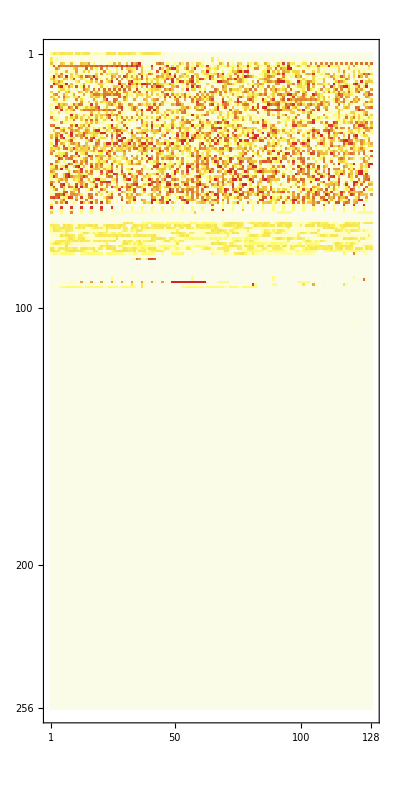

```mathematica
MatrixPlot[
BlockMap[#&,Map[#&,DeviceRead[device,{"read_mem",0,32*1024}]],128],
ColorFunction->"TemperatureMap"
]
```

#### Evaluate statistics of memory access

```mathematica
DeviceRead[device,{
"reset","/Users/ckorikov/_syntacore/projects/wolfram_russianhack18_scr1/cpp_bridge/dhrystone.bin"
}];
```

```mathematica
busData=Table[
DeviceRead[device,"step"];
DeviceRead[device,"get_data_bus"
],100000];
```

```mathematica
busDataClean=Select[busData,#[[1]]>0 &];
```

```mathematica
busDataCleanFull=Flatten[Map[
Range[
#[[1]],#[[1]]+(#[[2]]-1)
]&,
busDataClean]];
```

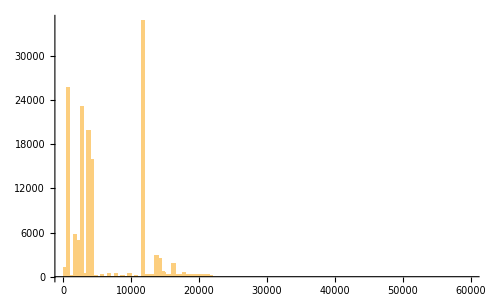

```mathematica
Histogram[busDataCleanFull,{0,60000,500}]
```

#### Develop new devices

```mathematica
DeviceRead[device,{
"reset","/Users/ckorikov/_syntacore/projects/wolfram_russianhack18_scr1/cpp_bridge/dhrystone.bin"
}];
```

```mathematica
branchstatelist=Table[
DeviceRead[device,"next_ipc"];
DeviceRead[device,"get_branch_state"],
20000
];
```

```mathematica
jumpsDataset=Select[branchstatelist,(#[[3]]+#[[4]]>0)&];
```

```mathematica
jumpsDataset//TableView
```

1:eJzt2rFLVVEcB/BbTysV1CE0RKTiIRHODeLQECEhEg4N0RQF0VDQ0CDh0CQN
IQ2N0iwhDU7NEeEQDQ0NESHR1F/QEJ3T7aLnh8KDwh72ufB4/D6c873Xy9eH
7+Kp63cX7hyuqurmcFX1pvexPKTjUP32a2aMMcYYY4wxxhhjjDHGGGOMMcYY
Y4wxxhhjjDHGGGOMMcYYY4wxxhhjjDHGGGOMMcYYY4wxxhhjjDHGGGOMMcYY
Y4wxxhhjjDHGGGOMMcYYY4wxxhhjjDHGGGOMMcYYY4wxxhhjjDHGGGOMMcYY
Y4wxxhhjjDHGGGOMMcYYO8jW/m2NZ1vsK9flebVVrltP87NgW2k+2Sr35rkd
1k236tdOm2ptn6PZm+etYFutzq9lJFi+lolg7T3OK0+ePHny5MmTJ0+ePHny
5DV5nX7XnQrrphhj/9z24xnUfjwPmxssLc+dXl+3f8bKkydPnjx58uTJkydP
njzPtBj7n+2gPL/q9Fq6/bNTnjx58g5a3nqwnPch2OyRqlo5Up43z5O9peX5
3Fi5txqvqvPBvqX5YrBPab48Vubl+VZY9yDNa2Fdnt8Hy/NMb7l3vqd+7VyX
548j5bqtE1X1NdjqaLruYCvJ+kdLm0jzldHyHHleDpbnbrpXS+G+5Hkx2KJ7
tee9ethT5uV79SSsy/OrYHnu9Hd1I+zd6LK8t+Ee5Dx//8mTJ0+ePHl/L8+z
XMa6z/7kWem7vnLv8mD67j1U2o00Xwp2O82Pg10drqrnwe4nexFsPNnrYPeS
be6y7nOwpWRfdln3PdijZD92WXd8uLSnw7UXlvadCTaT5ulgc2m+NrQ95yPP
C0fDfUlz+1i5Ls+b4f8s87zWX+6dTXY6/ByTaX7ZX+7N85uw9+xA53vz2p2W
5wsD5d75NE+FvXnWF33RF33RF33Rl3KdvuiLvuiLvtSHvuiLvuhLY/qiL/qi
L43pi77oS33oi77oi740pi/6oi/1oS/6oi/6oi/lOn3RF33RF32pD33RF33R
l8b0RV/0RV8a0xd90Zf60Bd90Rd9aUxf9EVf6kNf9EVf9KUb+vITz4Czhg==

Разбиваем на 2 выборки :

```mathematica
trainingSamples=Round[0.7*Length[jumpsDataset]];
```

Решаем задачу классификации на 2 класса

```mathematica
historyLen=20;
trainingData=Reap[
For[i=historyLen+1,i≤trainingSamples,i++,
Sow[jumpsDataset[[i-historyLen;;i-1,3]]->jumpsDataset[[i,3]]]]
][[2,1]];
classes={0,1};
```

Создаем простую сеть

```mathematica
bpNet=NetChain[
{LinearLayer[10],Ramp,LinearLayer[],SoftmaxLayer[]}
]
```

NetChain[]

Обучаем сеть

```mathematica
trainedNet=NetTrain[bpNet,trainingData,Method->"SGD"]
```

NetChain[]

Подготавливаем тестовую выборку

```mathematica
testData=Reap[
For[i=trainingSamples+1,i≤Length[jumpsDataset],i++,
Sow[jumpsDataset[[i-historyLen;;i-1,3]]->jumpsDataset[[i,3]]]]
][[2,1]];
```

Смотрим метрики

```mathematica
cm=ClassifierMeasurements[trainedNet,testData]
```

ClassifierMeasurementsObject[…]

```mathematica
cm["Accuracy"]
```

0.69579

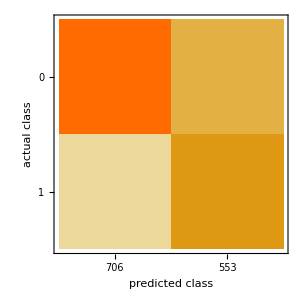

```mathematica
cm["ConfusionMatrixPlot"]
```

#### Work with assembler

```mathematica
asm=Select[Import["./programs/dhrystone21.dump","Lines"],StringLength[#]>0&];
```

```mathematica
DeviceRead[device,{
"reset","/Users/ckorikov/_syntacore/projects/wolfram_russianhack18_scr1/programs/dhrystone21.hex"
}];
labels=Select[Flatten[#,1]&@StringCases[asm,StartOfString~~Shortest[address:HexadecimalCharacter..]~~" <"~~Shortest[label__]~~">"~~Shortest[__]-> {address,label}],FromDigits[#[[1]],16]≠0&];
labelsHex=Sort[Map[{FromDigits[#[[1]],16],#[[2]]}&,labels],#1[[1]]<#2[[1]]&];
```

```mathematica
ipcList = Table[DeviceRead[device,"next_ipc"],150000];
```

```mathematica
colorLabels=BlockMap[{#[[1]][[2]],#[[1]][[1]],#[[2]][[1]]}&,Sort[labelsHex],2,1];
colorLabels=MapIndexed[Append[#1,ColorData["CMYKColors"][#2[[1]]/Length@colorLabels]]&,colorLabels];
getColor[b_]:=SelectFirst[colorLabels,#[[2]]≤b  && b ≤  #[[3]]&][[4]];
getName[b_]:=SelectFirst[colorLabels,#[[2]]≤b  && b ≤  #[[3]]&][[1]];
dataGraph=Union[
BlockMap[#[[1]]->#[[2]]&,Select[BlockMap[If[Abs[#[[1]]-#[[2]]]>4,#[[1]],0]&,ipcList,2,1 ],#>0&],2,1]
];
```

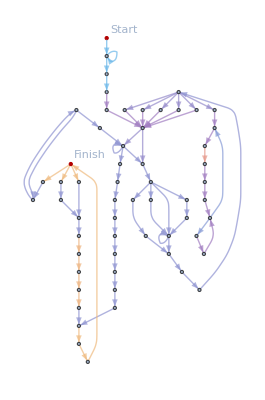

```mathematica
c=HighlightGraph[
dataGraph,
{
Labeled[(First@dataGraph)[[1]],"Start"],Labeled[(Last@dataGraph)[[1]],"Finish"],Map[Style[#,getColor[#[[1]]]]&,dataGraph],
Map[Tooltip[#,getName[#[[1]]]]&,dataGraph]
},
GraphLayout->"LayeredDigraphEmbedding"
]
```

#### Read signal (TBD)

## How it works

#### General Scheme

#### С++ wrapper

```mathematica
FilePrint["./cpp_bridge/test.cpp"]
```

#include "test.h"
#include "scr1_wrapper.h"

static SCR1::processor* p_proc;

mint
WolframLibrary_getVersion()
{
    return WolframLibraryVersion;
}

DLLEXPORT
int
WolframLibrary_initialize(WolframLibraryData libData)
{
    p_proc = new SCR1::processor;
    return 0;
}

void
WolframLibrary_uninitialize(WolframLibraryData libData)
{
    delete p_proc;
    return;
}

int
constantzero(WolframLibraryData libData, mint Argc, MArgument *Args, MArgument Res)
{
    MArgument_setInteger(Res, 0);
    return LIBRARY_NO_ERROR;
}

int
reset(WolframLibraryData libData, mint Argc, MArgument *Args, MArgument Res)
{
    int res = LIBRARY_NO_ERROR;
    const char *string = MArgument_getUTF8String(Args[0]);
    try {
        p_proc->reset(string);
    } catch (...) {
        res = LIBRARY_FUNCTION_ERROR;
    }
    return res;
}

int
run(WolframLibraryData libData, mint Argc, MArgument *Args, MArgument Res)
{
    int res = LIBRARY_NO_ERROR;
    try {
        p_proc->run();
    } catch (...) {
        res = LIBRARY_FUNCTION_ERROR;
    }
    return res;
}

int
step(WolframLibraryData libData, mint Argc, MArgument *Args, MArgument Res)
{
    int res = LIBRARY_NO_ERROR;
    try {
        p_proc->step();
    } catch (...) {
        res = LIBRARY_FUNCTION_ERROR;
    }
    return res;
}

int
is_finished(WolframLibraryData libData, mint Argc, MArgument *Args, MArgument Res)
{
    int res = LIBRARY_NO_ERROR;
    mbool state = p_proc->is_finished();
    // libData->Message("is_finished");
    MArgument_setBoolean(Res, state);
    return res;
}

int
get_pc(WolframLibraryData libData, mint Argc, MArgument *Args, MArgument Res)
{
    int res = LIBRARY_NO_ERROR;
    mint pc = p_proc->get_pc();
    MArgument_setInteger(Res, pc);
    return res;
}

int
next_pc(WolframLibraryData libData, mint Argc, MArgument *Args, MArgument Res)
{
    int res = LIBRARY_NO_ERROR;
    mint pc = p_proc->next_pc();
    MArgument_setInteger(Res, pc);
    return res;
}

int
get_register(WolframLibraryData libData, mint Argc, MArgument *Args, MArgument Res)
{
    int res = LIBRARY_NO_ERROR;
    int num = MArgument_getInteger (Args[0]);
    mint reg = p_proc->get_register(num);
    MArgument_setInteger(Res, reg);
    return res;
}

int
get_register_list(WolframLibraryData libData, mint Argc, MArgument *Args, MArgument Res)
{
    int res = LIBRARY_NO_ERROR;
    MTensor out_MT;
    const mint out_dim[]={31};
    mint out_rank=1;
    int err = libData->MTensor_new(MType_Integer, out_rank, out_dim, &out_MT);
    mint *out_cpointer=libData->MTensor_getIntegerData(out_MT);

    for (size_t i = 0; i < 32; i++) {
        out_cpointer[i]=p_proc->get_register(i);
    }

    MArgument_setMTensor(Res, out_MT);
    return res;
}

int
get_branch_state(WolframLibraryData libData, mint Argc, MArgument *Args, MArgument Res)
{
    int res = LIBRARY_NO_ERROR;
    MTensor out_MT;
    const mint out_dim[]={5};
    mint out_rank=1;
    int err = libData->MTensor_new(MType_Integer, out_rank, out_dim, &out_MT);
    mint *out_cpointer=libData->MTensor_getIntegerData(out_MT);

    out_cpointer[0] = p_proc->get_pc();
    out_cpointer[1] = p_proc->get_jump_state();
    out_cpointer[2] = p_proc->get_branch_taken_state();
    out_cpointer[3] = p_proc->get_branch_not_taken_state();
    out_cpointer[4] = p_proc->get_jb_addr_state();

    MArgument_setMTensor(Res, out_MT);
    return res;
}

int
read_memory(WolframLibraryData libData, mint Argc, MArgument *Args, MArgument Res)
{
    int res = LIBRARY_NO_ERROR;
    int addr = MArgument_getInteger (Args[0]);
    int length = MArgument_getInteger (Args[1]);
    MTensor out_MT;
    const mint out_dim[]={length};
    mint out_rank=1;
    int err = libData->MTensor_new(MType_Integer, out_rank, out_dim, &out_MT);
    mint *out_cpointer=libData->MTensor_getIntegerData(out_MT);

    for (size_t i = 0; i < length; i++) {
        out_cpointer[i]=p_proc->read_mem(addr+i);
    }

    MArgument_setMTensor(Res, out_MT);
    return res;
}

int
read_dmem_bus(WolframLibraryData libData, mint Argc, MArgument *Args, MArgument Res)
{
    int res = LIBRARY_NO_ERROR;
    MTensor out_MT;
    const mint out_dim[]={2};
    mint out_rank=1;
    int err = libData->MTensor_new(MType_Integer, out_rank, out_dim, &out_MT);
    mint *out_cpointer=libData->MTensor_getIntegerData(out_MT);

    out_cpointer[0] = p_proc->read_dmem_bus_addr();
    out_cpointer[1] = p_proc->read_dmem_bus_bytewidth();

    MArgument_setMTensor(Res, out_MT);
    return res;
}

```mathematica
FilePrint["./cpp_bridge/test.h"]
```

#include "WolframLibrary.h"

#ifdef __cplusplus
extern "C"
{
#endif

DLLEXPORT mint
WolframLibrary_getVersion();

DLLEXPORT
int
WolframLibrary_initialize(WolframLibraryData libData);

DLLEXPORT
int
constantzero(WolframLibraryData libData, mint Argc, MArgument *Args, MArgument Res);

DLLEXPORT
int
reset(WolframLibraryData libData, mint Argc, MArgument *Args, MArgument Res);

DLLEXPORT
int
run(WolframLibraryData libData, mint Argc, MArgument *Args, MArgument Res);

DLLEXPORT
int
step(WolframLibraryData libData, mint Argc, MArgument *Args, MArgument Res);

DLLEXPORT
int
is_finished(WolframLibraryData libData, mint Argc, MArgument *Args, MArgument Res);

DLLEXPORT
int
get_pc(WolframLibraryData libData, mint Argc, MArgument *Args, MArgument Res);

DLLEXPORT
int
next_pc(WolframLibraryData libData, mint Argc, MArgument *Args, MArgument Res);

DLLEXPORT
int
get_register(WolframLibraryData libData, mint Argc, MArgument *Args, MArgument Res);

DLLEXPORT
int
get_register_list(WolframLibraryData libData, mint Argc, MArgument *Args, MArgument Res);

DLLEXPORT
int
get_branch_state(WolframLibraryData libData, mint Argc, MArgument *Args, MArgument Res);

DLLEXPORT
int
read_memory(WolframLibraryData libData, mint Argc, MArgument *Args, MArgument Res);

DLLEXPORT
int
read_dmem_bus(WolframLibraryData libData, mint Argc, MArgument *Args, MArgument Res);

#ifdef __cplusplus
}
#endif

```mathematica
FilePrint["./cpp_bridge/scr1_wrapper.cpp"]
```

#include "scr1_wrapper.h"

#include <stdio.h>

uint64_t main_time;       // Current simulation time

double sc_time_stamp () {       // Called by $time in Verilog
   return main_time;           // converts to double, to match
}

namespace SCR1
{

    processor::processor()
    {
        this->top = new Vscr1_top_tb_axi;
    }

    processor::~processor()
    {
        this->top->final();
        delete this->top;
    }

    void processor::reset(const char * mem)
    {
        Verilated::commandArgs(1, &mem);
        this->top->rst_n=0;
        this->step();
        this->top->rst_n=1;
    }

    void processor::step()
    {
        this->top->clk = 1;
        for (size_t i = 0; i < 10; i++)
        {
            if(!Verilated::gotFinish())
            {
                this->top->eval();
                main_time++;
            } else {
                break;
            }
        }
        this->top->clk = 0;
        for (size_t i = 0; i < 10; i++)
        {
            if(!Verilated::gotFinish())
            {
                this->top->eval();
                main_time++;
            } else {
                break;
            }
        }

    }

    void processor::run()
    {
        while(!Verilated::gotFinish())
        {
            this->step();
        }
    }

    bool processor::is_finished()
    {
        return Verilated::gotFinish();
    }

    int processor::get_pc()
    {
        return this->top->pc;
    }

    int processor::next_pc()
    {
        int pc = this->get_pc();
        while(!Verilated::gotFinish())
        {
            this->step();
            int current_pc = this->get_pc();
            if (current_pc != pc)
            {
                pc = current_pc;
                break;
            }
        }
        return pc;
    }

    int processor::get_register(int num)
    {
        /* Rewrite it! */
        switch (num) {
            case 1: return this->top->gpr_x01;
            case 2: return this->top->gpr_x02;
            case 3: return this->top->gpr_x03;
            case 4: return this->top->gpr_x04;
            case 5: return this->top->gpr_x05;
            case 6: return this->top->gpr_x06;
            case 7: return this->top->gpr_x07;
            case 8: return this->top->gpr_x08;
            case 9: return this->top->gpr_x09;
            case 10: return this->top->gpr_x10;
            case 11: return this->top->gpr_x11;
            case 12: return this->top->gpr_x12;
            case 13: return this->top->gpr_x13;
            case 14: return this->top->gpr_x14;
            case 15: return this->top->gpr_x15;
            case 16: return this->top->gpr_x16;
            case 17: return this->top->gpr_x17;
            case 18: return this->top->gpr_x18;
            case 19: return this->top->gpr_x19;
            case 20: return this->top->gpr_x20;
            case 21: return this->top->gpr_x21;
            case 22: return this->top->gpr_x22;
            case 23: return this->top->gpr_x23;
            case 24: return this->top->gpr_x24;
            case 25: return this->top->gpr_x25;
            case 26: return this->top->gpr_x26;
            case 27: return this->top->gpr_x27;
            case 28: return this->top->gpr_x28;
            case 29: return this->top->gpr_x29;
            case 30: return this->top->gpr_x30;
            case 31: return this->top->gpr_x31;
            default: return 0;
        }
    }

    int processor::get_jump_state()
    {
        return this->top->jump;
    }

    int processor::get_branch_taken_state()
    {
        return this->top->branch_taken;
    }

    int processor::get_branch_not_taken_state()
    {
        return this->top->branch_not_taken;
    }

    int processor::get_jb_addr_state()
    {
        return this->top->jb_addr;
    }

    int processor::read_mem(int address)
    {
        if (address >= 0 && address <= MAX_ADDR)
        {
            return this->top->scr1_top_tb_axi__DOT__i_memory_tb__DOT__memory[address];
        }
        else
        {
            return 0;
        }
    }

    void processor::write_mem(int address, int data)
    {
        if (address >= 0 && address <= MAX_ADDR)
        {
            this->top->scr1_top_tb_axi__DOT__i_memory_tb__DOT__memory[address] = data;
        }
    }

    int processor::read_dmem_bus_addr()
    {
        return this->top->ls_addr;
    }

    int processor::read_dmem_bus_bytewidth()
    {
        switch (this->top->ls_width)
        {
            case 0: return 1;
            case 2: return 2;
            case 3: return 4;
            default: return 0;
        }
    }
}

```mathematica
FilePrint["./cpp_bridge/scr1_wrapper.h"]
```

#ifndef SCR1_WRAPPER_H
#define SCR1_WRAPPER_H

#include <verilated.h>                      // Defines common routines
#include "Vscr1_top_tb_axi.h"               // From Verilating "top.v"

#define MAX_ADDR 32768

double sc_time_stamp ();
extern uint64_t main_time;

namespace SCR1
{
    class processor {
        Vscr1_top_tb_axi *top;
        public:
            processor();
            ~processor();
            void step();
            void reset(const char * mem);
            int get_pc();
            void run();
            bool is_finished();
            int next_pc();
            int get_register(int num);
            int get_jump_state();
            int get_branch_taken_state();
            int get_branch_not_taken_state();
            int get_jb_addr_state();
            int read_mem(int address);
            void write_mem(int address, int data);
            int read_dmem_bus_addr();
            int read_dmem_bus_bytewidth();
    };
}

#endif SCR1_WRAPPER_H